```mathematica
Quit[]
```

```mathematica
A0[z_]=1/Sqrt[2k] E^(π xi/2)W[z];
AS[z_]=1/Sqrt[2k] E^(π xi/2)z^(SigmaEin/2)(c1 WS[z]+c2 MS[z]);
```

```mathematica
Solve[A0[γ]==AS[γ]&&A0'[γ]==AS'[γ],{c1,c2}]
```

{{c1→(γ^(-1-SigmaEin/2) (-SigmaEin MS[γ] W[γ]-2 γ W[γ] MS'[γ]+2 γ MS[γ] W'[γ]))/(2 (-WS[γ] MS'[γ]+MS[γ] WS'[γ])),c2→(γ^(-1-SigmaEin/2) (-SigmaEin W[γ] WS[γ]+2 γ WS[γ] W'[γ]-2 γ W[γ] WS'[γ]))/(2 (WS[γ] MS'[γ]-MS[γ] WS'[γ]))}}

```mathematica
$Assumptions={z>0,xi>0,xe>0,-1≤cos≤1,SigmaBin>0,SigmaEin>0,k>0,γ>0};
```

```mathematica
xieff[xi_,cos_,SigmaBin_]=xi-1/2 SigmaBin (1-cos^2)//Simplify;
```

```mathematica
W[z_,xi_]=WhittakerW[-I xi,1/2,-2I z];
Wp[z_,xi_]=D[W[z,xi], z]//Simplify;
WS[z_,xe_,SigmaEin_]=WhittakerW[-I xe,(1+SigmaEin)/2,-2I z]//Simplify;
WSp[z_,xe_,SigmaEin_]=D[WS[z,xe,SigmaEin], z]//Simplify;
MS[z_,xe_,SigmaEin_]=WhittakerM[-I xe,(1+SigmaEin)/2,-2I z]//Simplify;
MSp[z_,xe_,SigmaEin_]=D[MS[z,xe,SigmaEin], z]//Simplify;
```

```mathematica
Wronskian[{WhittakerW[-I xe,1/2,-2I z],WhittakerM[-I xe,1/2,-2I z]},z]
```

-2 (ⅈ+xe) Hypergeometric1F1[2-ⅈ xe,2,2 ⅈ z] HypergeometricU[ⅈ xe,0,-2 ⅈ z]-4 z Hypergeometric1F1[1-ⅈ xe,2,2 ⅈ z] HypergeometricU[ⅈ xe,2,-2 ⅈ z]

```mathematica
-WS[γ,xe,SigmaEin]MSp[γ,xe,SigmaEin]+MS[γ,xe,SigmaEin]WSp[γ,xe,SigmaEin]/.{γ->2 8,xe->8,SigmaEin->6.965}
```

1.82711×10^6+362165. ⅈ

```mathematica
(2I Gamma[SigmaEin+2])/Gamma[1+I xe+SigmaEin/2]/.{γ->2 8,xe->8,SigmaEin->6.965}
```

1.82711×10^6+362165. ⅈ

```mathematica
c1[xi_,xe_,SigmaEin_]=γ^(-SigmaEin/2)Gamma[1+I xe+SigmaEin/2]/(2I Gamma[SigmaEin+2])(Wp[γ,xi]MS[γ,xe,SigmaEin]-W[γ,xi]MSp[γ,xe,SigmaEin]-SigmaEin/(2γ)W[γ,xi]MS[γ,xe,SigmaEin])/.{γ->2xe}//Simplify;
c2[xi_,xe_,SigmaEin_]=-γ^(-SigmaEin/2)Gamma[1+I xe+SigmaEin/2]/(2I Gamma[SigmaEin+2])(Wp[γ,xi]WS[γ,xe,SigmaEin]-W[γ,xi]WSp[γ,xe,SigmaEin]-SigmaEin/(2γ)W[γ,xi]WS[γ,xe,SigmaEin])/.{γ->2xe}//Simplify;
```

```mathematica
PBBoH4[z_,xi_,xe_,SigmaEin_]=1/(4 π^2)E^(π xi)z^(4+SigmaEin)Abs[c1[xi,xe,SigmaEin]WS[z,xe,SigmaEin]+c2[xi,xe,SigmaEin]MS[z,xe,SigmaEin]]^2//Simplify;
PEEoH4[z_,xi_,xe_,SigmaEin_]=1/(4 π^2)E^(π xi)z^(4+SigmaEin)Abs[c1[xi,xe,SigmaEin]WSp[z,xe,SigmaEin]+c2[xi,xe,SigmaEin]MSp[z,xe,SigmaEin]+SigmaEin/(2z)(c1[xi,xe,SigmaEin]WS[z,xe,SigmaEin]+c2[xi,xe,SigmaEin]MS[z,xe,SigmaEin])]^2//Simplify;
```

```mathematica
intzPBBoH4[xi_,xe_,SigmaEin_]:=NIntegrate[PBBoH4[E^logz,xi,xe,SigmaEin],{logz,-2Log[10],Log[2xe]}]
intzPEEoH4[xi_,xe_,SigmaEin_]:=NIntegrate[PEEoH4[E^logz,xi,xe,SigmaEin],{logz,-2Log[10],Log[2xe]}]
```

```mathematica
ListintzPBBoH4=ParallelTable[{cos,intzPBBoH4[xi,xieff[xi,cos,SigmaBin],SigmaEin]/.{xi->8,SigmaBin->5.59,SigmaEin->6.965}//Quiet},{cos,0,1,1/100}];//AbsoluteTiming
```

{106.018,Null}

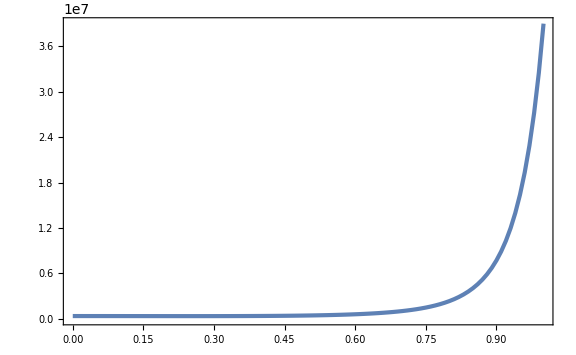

```mathematica
ListPlot[ListintzPBBoH4,PlotRange->Full]
```

```mathematica
dcos=1/50
```

1/50

```mathematica
rhoBoH4[xi_,SigmaBin_,SigmaEin_]:=2 dcos/4(ParallelSum[intzPBBoH4[xi,xieff[xi,cos,SigmaBin],SigmaEin],{cos,dcos,1-dcos,dcos}]
+(intzPBBoH4[xi,xieff[xi,0,SigmaBin],SigmaEin]+intzPBBoH4[xi,xieff[xi,1,SigmaBin],SigmaEin])/2)
rhoEoH4[xi_,SigmaBin_,SigmaEin_]:=2 dcos/4(ParallelSum[intzPEEoH4[xi,xieff[xi,cos,SigmaBin],SigmaEin],{cos,dcos,1-dcos,dcos}]
+(intzPEEoH4[xi,xieff[xi,0,SigmaBin],SigmaEin]+intzPEEoH4[xi,xieff[xi,1,SigmaBin],SigmaEin])/2)
```

```mathematica
SigmaEout[rBoH4_,rEoH4_]=e^3/(6 π^2)Sqrt[2rBoH4]Coth[π Sqrt[rBoH4/rEoH4]]/.{e->0.55}//Simplify;
SigmaBout[rBoH4_,rEoH4_]=e^3/(6 π^2)Sqrt[2rEoH4]Coth[π Sqrt[rBoH4/rEoH4]]/.{e->0.55}//Simplify;
```

```mathematica
rBoH4t=rhoBoH4[8,5.59,6.965];//AbsoluteTiming
rEoH4t=rhoEoH4[8,5.59,6.965];//AbsoluteTiming
rBoH4t
rEoH4t
SigmaEout[rBoH4t,rEoH4t]
SigmaBout[rBoH4t,rEoH4t]
```

{32.1672,Null}

{54.,Null}

1.40124×10^6

3.12419×10^6

4.84542

7.23509